# Neural Logic

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
?neurallogic`*
```

## Utilities

```mathematica
HardPrediction[m_]:=Ordering[(With[{t=#[True]},If[MissingQ[t],0,t]]&)/@Counts/@m,-1]
HardTarget[t_]:=Flatten[Position[t,True]]
HardResults[hardPredictionTargetPairs_]:=Module[{results,accuracy},
results=Reverse[Sort[Counts[{HardPrediction[First[#]][[1]],HardTarget[Last[#]][[1]]}&/@hardPredictionTargetPairs]]];
accuracy=KeySelect[results,First[#]==Last[#]&];
{"Accuracy = "<>ToString[Total[accuracy]/Length[hardPredictionTargetPairs]*100.0]<>"%",results}
]
```

```mathematica
HardPrediction[{{True,False,False},{False,False,False},{True,True,False}}]
```

{3}

```mathematica
HardPrediction[{{True,False,False},{True,False,False},{False,False,False}}]
```

{2}

```mathematica
HardPrediction[{{True,True,False},{True,False,False},{True,True,True}}]
```

Null

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=10;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->Soften[Boole[With[{r=bf@@x},{r,!r}]]]]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

1024

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,250,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralNAND[250,classificationLayerSize,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=8*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,50],
HardDropoutLayer[0.25],
HardNeuralMajority[50,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=NetGraph[<|"NeuralLogicNet"->net,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"}]
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[softNet,trainData,All,
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

```mathematica
trainedSoftNet=NetExtract[result["TrainedNet"],"NeuralLogicNet"]
```

NetChain[<>]

```mathematica
NetFlatten[trainedSoftNet]
```

NetGraph[<>]

### Evaluate soft net

```mathematica
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 62.5%
<|{2,2}→19,{2,1}→12,{1,1}→6,{1,2}→3|>

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 95.%
<|{2,2}→21,{1,1}→17,{1,2}→1,{2,1}→1|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 5.2 kilobytes
Hard net size = 0.1625 kilobytes
Saving factor = 32.

```mathematica
boolNet=hnf[Table[Symbol["b"<>ToString[i]],{i,1,inputSize}]]
```

```mathematica
BooleanConvert[boolNet]
```

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"../data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,1,0,0},-Graphics-→{0,0,0,1},-Graphics-→{0,0,0,1},-Graphics-→{0,0,0,1},-Graphics-→{0,0,0,1}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Standard neural net

```mathematica
ConvertDataToClasses[data_]:=MapAt[First[Flatten[Position[#,1]]]-1&,data,{All,2}]
```

### Create net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```

### Train net

```mathematica
result=NetTrain[net,ConvertDataToClasses[trainData],All,
ValidationSet->{ConvertDataToClasses[RandomSample[testData,UpTo[1000]]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate net

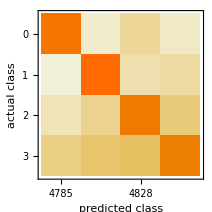
Classifier Measurements
Classifier method | Net
Number of test examples | 19803
Accuracy | (94.180.17) %
Accuracy baseline | (27.570.32) %
Geometric mean of probabilities | 0.449 ± 0.00065
Mean cross entropy | 0.802 ± 0.0014
Single evaluation time | 2.1 ms/example
Batch evaluation speed | 144. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]
```

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,100,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralAND[100,classificationLayerSize,RandomBalancedNormalSoftBits[#]&],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=64*numClasses},
HardNeuralChain[
{
HardNeuralMajority[inputSize,classificationLayerSize],
HardDropoutLayer[0.25],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}
]
];
```

```mathematica
softNet=NetGraph[<|"NeuralLogicNet"->net,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"}];
```

```mathematica
softNet
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[softNet,trainData,All,
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->4000];
```

```mathematica
trainedSoftNet=NetExtract[result["TrainedNet"],"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
(*ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]*)
```

```mathematica
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 88.7088%
<|{2,2}→5049,{1,1}→4417,{4,4}→4083,{3,3}→4018,{3,4}→376,{2,4}→353,{4,3}→303,{2,3}→265,{4,2}→182,{3,2}→178,{4,1}→166,{1,3}→143,{3,1}→136,{1,4}→90,{2,1}→27,{1,2}→17|>

```mathematica
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
```

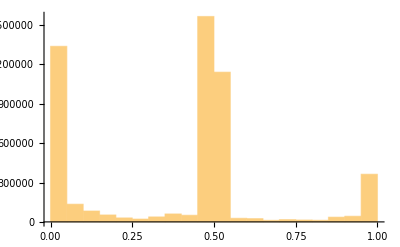

```mathematica
Histogram[Flatten[First/@softPredictionTargetPairs],PlotRange->All]
```

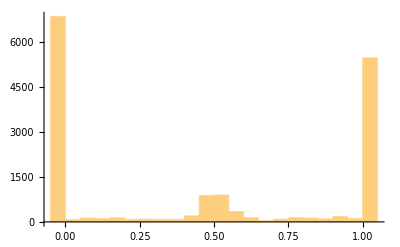

```mathematica
Histogram[Flatten[ExtractWeights[trainedSoftNet]],PlotRange->All]
```

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 88.7088%
<|{2,2}→5049,{1,1}→4417,{4,4}→4083,{3,3}→4018,{3,4}→376,{2,4}→353,{4,3}→303,{2,3}→265,{4,2}→182,{3,2}→178,{4,1}→166,{1,3}→143,{3,1}→136,{1,4}→90,{2,1}→27,{1,2}→17|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 65.536 kilobytes
Hard net size = 2.048 kilobytes
Saving factor = 32.

```mathematica
boolNet=hnf[Table[Symbol["b"<>ToString[i]],{i,1,inputSize}]]
```

## Notes

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
NetFlatten[HardNeuralAND[2,4][[1]]]
```

NetGraph[<>]

```mathematica
f[x_List]:=Block[{min=Min[x],mean},
mean=Mean[x];
If[min>1/2,
min+(((min-1/2)mean)(1-min))^2,
min+((1/2-min)mean)^2]
]
```

```mathematica
Manipulate[
Plot[
{f[{x1,x2,x3,x4,x5}],x2,x3,x4,x5},
{x1,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic,PlotLegends->Automatic
],
{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1}
]
```

```mathematica
HardMinAll[]:=NetGraph[
<|
"Min"->AggregationLayer[Min],
"Mean"->AggregationLayer[Mean],
"Filter"->FunctionLayer[
If[#Min>1/2,
#Min+((#Min-1/2)#Mean)(1-#Min),
#Min+(1/2-#Min)#Mean
]&
]
|>,
{
"Min"->NetPort["Filter","Min"],
"Mean"->NetPort["Filter","Mean"]
}
]
```

```mathematica
hma=HardMinAll[]
```

NetGraph[<>]

```mathematica
hma[{{0.1,0.6,0.8},{0.9,0.9,0.52},{0.1,0.01,0.45},{0.1,0.01,0.55},{0.55,0.57,0.9}}]
```

{0.3,0.527424,0.101467,0.1178,0.56515}

## Counting

```mathematica
(* Experimental *)
net=With[{classificationLayerSize=32*numClasses},
NetGraph[
<|
"Layer1"->HardNeuralNAND[inputSize,600][[1]],
"Layer2"->HardNeuralNAND[600,classificationLayerSize][[1]],
"ToMatrix"->ReshapeLayer[{1,classificationLayerSize}],
"Require"->Require[HardNeuralLTEK[1,classificationLayerSize,32][[1]]][[1]],
"ToVector"->ReshapeLayer[{classificationLayerSize}],
"ClassPredictions"->HardNeuralPortLayer[classificationLayerSize,numClasses][[1]]
|>,
{
"Layer1"->"Layer2",
"Layer2"->"ToMatrix",
"ToMatrix"->"Require",
"Require"->"ToVector",
"ToVector"->"ClassPredictions"
}
]]
```